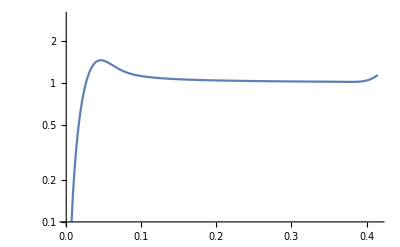

```mathematica
Clear["Global`*"];
(*Stationary state solution to the diffusion equation*)(*Appendix A.1 Colafrancesco et.al. (2006)*)
 


(*radv = .003;   (*Characteristic distance (Mpc) NOTE: dependent on E, may need modification*)
*)

r1 = .001;  (*some radius (Mpc)*)
r2 = .005;
r3 = .01;
r4= .05;  
r5 = .1;
r6 = .2;
r7 = .5;

rh = .415;    (*Coma Halo radius (Mpc) from Storm et. al. 2103*)
rs = .404;  (*Coma Scale radius (Mpc),from Jfactor Mathematica code*)

rn[n_,r_]:= (-1)^n*r +2*n*rh ; (*Image radii, Colafrancesco et. al. 2006*)

nx[p_]:=1/(p*(1+p/rs)^2); 
(*NFW profile as placeholder*)

G[radv_,r_] := 1/(Sqrt[4*Pi]*radv)Sum[
NIntegrate[(x/rn[i,r])*(Exp[-(x-rn[i,r])^2/(4*radv^2)]-Exp[-(x+rn[i,r])^2/(4*radv^2)])(nx[x]/nx[r])^2,{x,0,rh},AccuracyGoal->50],{i,-20,20}];
(*LogPlot[{G[t,r1],G[t,r2],G[t,r3],G[t,r4],G[t,r5],G[t,r6],G[t,r7]},{t,0,.04},PlotRange->{1/10,10},PlotLegends->{"r = 1kpc","r = 5kpc","r = 10kpc","r = 50kpc","r = 100kpc","r = 200kpc","r = 500kpc"}]*)
LogPlot[G[.015,r],{r,0,.415},PlotRange-> {.1,3}]
```

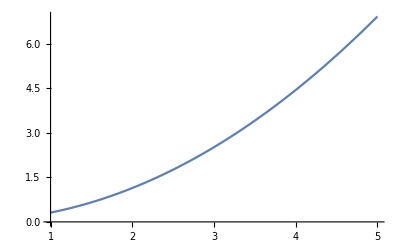

```mathematica
(*Energyloss term, dndeeq*)
(*Energy loss coefficients in (10^-6 Gev/s) for inverse compton, synchrotron, coulomb scattering, and brem. from Cola. 2006*)
bic0 = .25;
bsyn0 = .0254;
bcoul0 = 6.13;
bbrem0 = 1.51;
Bmu = 1;(* Magnetic field in micro Gauss*)
n = .0013; (*mean number of electrons (Density averaged over space)*)
m = .000511; (*electron mass Gev*)
(*y = E/m unused*)

b[E_]:= bic0*E^2+bsyn0*Bmu^2*E^2+bcoul0*n*(1+Log[E/(m*n)]/75) +bbrem0*n*(.36+Log[E/(m*n)]); 
Plot[b[E],{E,1,5}]
```